```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

Figure 3 from Dors and Kletzing [1999]

```mathematica
nmPlot=1;TmPlot=500; (*in cm^-3 and eV, respectively*)
```

```mathematica
plotKappas={22/10,3,5};
plotRBs={3,10,30,100,10*^6};
plotter=Flatten[Function[x,(((JEVKappaPhiBar[phiBar,x,Tm,nm,#])&/@plotKappas)~Join~{JEVMaxwellianPhiBar[phiBar,x,Tm,nm]})/.{Tm->TmPlot,nm->nmPlot}]/@plotRBs];
```

```mathematica
RBCols={Red,Green,Blue,Orange,Black};
kappaStyles={Dotted,Dashed,DotDashed,Automatic};
styles=Thread@Directive@Tuples[{RBCols,kappaStyles}];
```

```mathematica
{Sort@Flatten@Table[plotRBs,Length@plotKappas+1],Flatten@Riffle[Table[NumberForm[N@plotKappas,{3,1}],Length@plotRBs],"Maxwellian"]}
```

{{3,3,3,3,10,10,10,10,30,30,30,30,100,100,100,100,10000000,10000000,10000000,10000000},{{2.2,3.0,5.0},Maxwellian,{2.2,3.0,5.0},Maxwellian,{2.2,3.0,5.0},Maxwellian,{2.2,3.0,5.0},Maxwellian,{2.2,3.0,5.0}}}

```mathematica
{Sort@Flatten@Table[plotRBs,Length@plotKappas+1],Flatten@Riffle[Table[StringForm["κ = `1`",NumberForm[#,{3,1}]]&/@(N@plotKappas),Length@plotRBs],"Maxwellian",{2,-1,2}]}
```

{{3,3,3,3,10,10,10,10,30,30,30,30,100,100,100,100,10000000,10000000,10000000,10000000},{κ = 2.2,κ = 3.0,κ = 5.0,Maxwellian,κ = 2.2,κ = 3.0,κ = 5.0,Maxwellian,κ = 2.2,κ = 3.0,κ = 5.0,Maxwellian,κ = 2.2,κ = 3.0,κ = 5.0,Maxwellian,κ = 2.2,κ = 3.0,κ = 5.0,Maxwellian}}

```mathematica
plotLegStr=MapThread[(StringForm["RB = `1`, `2`",#1,#2])&,{Sort@Flatten@Table[plotRBs,Length@plotKappas+1],Flatten@Riffle[Table[StringForm["κ = `1`",NumberForm[#,{3,1}]]&/@(N@plotKappas),Length@plotRBs],"Maxwellian",{2,-1,2}]}]
```

{RB = 3, κ = 2.2,RB = 3, κ = 3.0,RB = 3, κ = 5.0,RB = 3, Maxwellian,RB = 10, κ = 2.2,RB = 10, κ = 3.0,RB = 10, κ = 5.0,RB = 10, Maxwellian,RB = 30, κ = 2.2,RB = 30, κ = 3.0,RB = 30, κ = 5.0,RB = 30, Maxwellian,RB = 100, κ = 2.2,RB = 100, κ = 3.0,RB = 100, κ = 5.0,RB = 100, Maxwellian,RB = 10000000, κ = 2.2,RB = 10000000, κ = 3.0,RB = 10000000, κ = 5.0,RB = 10000000, Maxwellian}

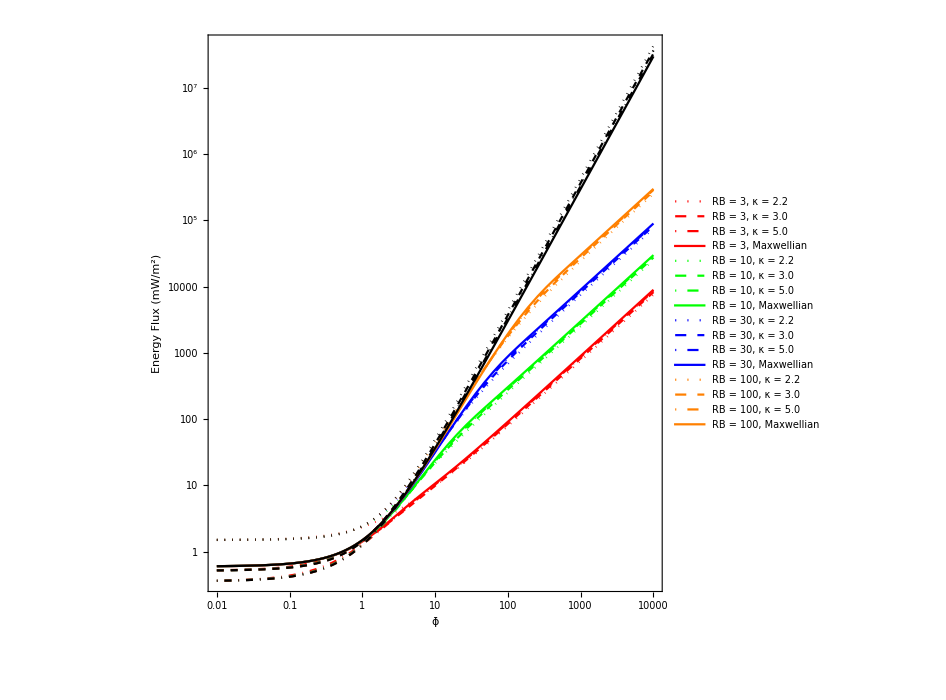

```mathematica
LogLogPlot[plotter,{phiBar,1/100,10000},PlotStyle->styles,Frame->True,FrameStyle->(FontSize->18),FrameLabel->{ϕ̄,"Energy Flux (mW/m^2)"},AspectRatio->1,PlotLegends->plotLegStr,ImageSize->700]
```